# Raman Transition

```mathematica
ClearAll@g
```

```mathematica
k=100;
m=0;
n=0;
g=1;
end=500;
```

```mathematica
sol=NDSolve[{ⅈ a'[x]==g/2 e[x](ⅇ^(-ⅈ k g x)+ⅇ^(-ⅈ (k+n) g x)),ⅈ b'[x]==g/2 e[x](ⅇ^(-ⅈ (k-m) g x)+ⅇ^(-ⅈ (k+n-m) g x)),ⅈ e'[x]==g*/2 (a[x](ⅇ^(ⅈ k g x)+ⅇ^(ⅈ (k+n) g x))+b[x](ⅇ^(ⅈ (k-m) g x)+ⅇ^(ⅈ (k+n-m) g x))),a[0]==1,b[0]==0,e[0]==0},{a,b,e},{x,0,1000}];
```

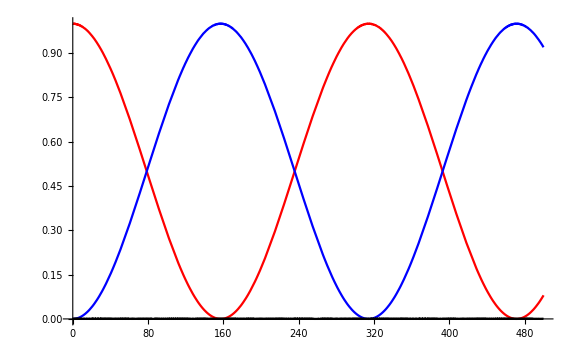

```mathematica
Show[Plot[((Norm@a[x])^2/.Flatten@sol),{x,0,end},PlotRange->All,ImageSize->Large,PlotStyle->Red],Plot[((Norm@b[x])^2/.Flatten@sol),{x,0,end},PlotRange->All,ImageSize->Large,PlotStyle->Blue],Plot[((Norm@e[x])^2/.Flatten@sol),{x,0,end},PlotRange->All,ImageSize->Large,PlotStyle->Black]]
```